```mathematica
SetDirectory[NotebookDirectory[]];
```

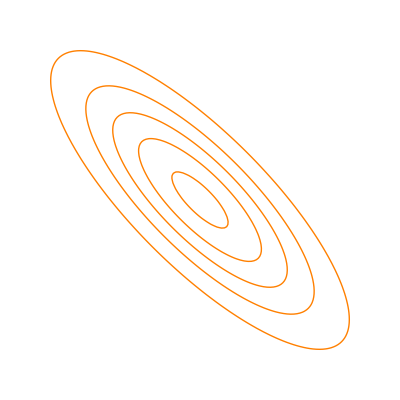

```mathematica
g1=ContourPlot[PDF[MultinormalDistribution[{0,0},{{1,-0.8},{-0.8,1}}],{x,y}],{x,-2, 2},{y,-2,2},ContourShading->None,PlotPoints->50,ContourStyle->Directive[Orange,Thick],Frame->None]
```

```mathematica
Export["coin_density.png",g1,Background->None]
```

coin_density.png